# Lineare Regression nach Gewichtung der Fehler (VL Lineare Regression Kießling, Ersteller: Moritz Siebert):

## Festlegung der Startbedingungen:

```mathematica
u=10^-3;
xvalues={0.9980(*,1.9910*),1.5230,0.6530}*10^-3;
yvalues={0.4082(*,0.46344*),0.42163,0.405011};
xvaluesall={0.9980,1.9910,1.5230,0.6530}*10^-3;
yvaluesall={0.4082,0.46344,0.41263,0.405011};
errys={0.0058,0.0078,0.020};(*errys can't be {}or 0*)
n:=Length[xvalues]
h=0.5;
R=23.75*10^-3;
t={60.96,(*16.8,*)28.44,136.4};
masses={0.01048(*,0.08500*),0.03612,0.00300}*10^-3;
```

## Ergebnisse der Linearen Regression

```mathematica
Dynamic[Panel[Style[
Column[
{Row[{"x_0 = ",f[0]}],
Row[{"b = ",  b}],
Row[{"σ_a = ",σa}],
Row[{"σ_b = ", σb}],
Row[{}],
Row[{"f(x) = ",a, If[b>0,"+"," "],b,"x"}]
}]
,FontSize->20]
]
]
```

## Benennung einzelner Variablen:

```mathematica
ClearAll[ysumwe,xsquasumwe,xsumwe,xysumwe,errsquasum,Δ,i]

ysumwe:=Sum[yvalues[[i]]/errys[[i]]^2,{i,1,n}]
xsumwe:=Sum[xvalues[[i]]/errys[[i]]^2,{i,1,n}]
xsquasumwe:=Sum[xvalues[[i]]^2/errys[[i]]^2,{i,1,n}]
xysumwe:=Sum[(xvalues[[i]] yvalues[[i]])/errys[[i]]^2,{i,1,n}]
errsquasum:=Sum[1/errys[[i]]^2,{i,1,n}]
Δ:=errsquasum*xsquasumwe-(xsumwe^2)
```

## Rechenweg für lineare Regression:

```mathematica
f[x_]:=a +b x 
a:=1/Δ(ysumwe*xsquasumwe-xsumwe*xysumwe)
b:=1/Δ(errsquasum*xysumwe-xsumwe*ysumwe)
σa:=√(1/Δ(xsquasumwe))
σb:=√(1/Δ errsquasum)
```

## Reynoldszahlen:

```mathematica
Rey[t_,η_,r_,m_]:=h/t*975*r/η
Reynolsnumbers=Table[Rey[t[[i]],yvalues[[i]],xvalues[[i]],masses[[i]]],{i,1,Length[xvalues]}]
```

{0.0195518,0.124665,0.063268,0.00576244}

## Plots:

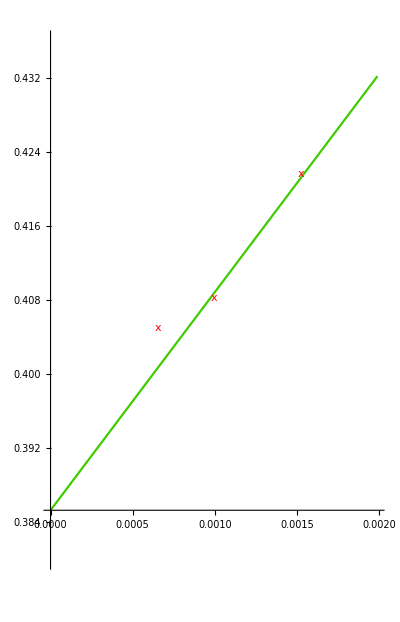

```mathematica
PlotGer:=Plot[f[x],{x,Min[xvalues[[1]],0],Max[xvaluesall]},PlotStyle->RGBColor[0.25,0.8,0]];
PlotPoin:=ListPlot[
Table[{xvalues[[i]],yvalues[[i]]},{i,1,n}],
	PlotStyle->Red,PlotMarkers->"x"]
Plotpoinall:=ListPlot[Table[{xvaluesall[[i]],yvaluesall[[i]]},{i,1,n}],PlotStyle->Magenta,PlotMarkers->"x"]
Mitallen:=Show[PlotGer,PlotPoin,Plotpoinall, ImageSize->{1000,800},PlotRange->{Min[yvalues*0.9],Max[yvaluesall*1.01]}]
NurmitkleinenReynoldszahlen:=Show[PlotGer,PlotPoin,AspectRatio->28/18,PlotRange->{0.38,0.436}]
NurmitkleinenReynoldszahlen
```

## Ladenburgkorrektur:

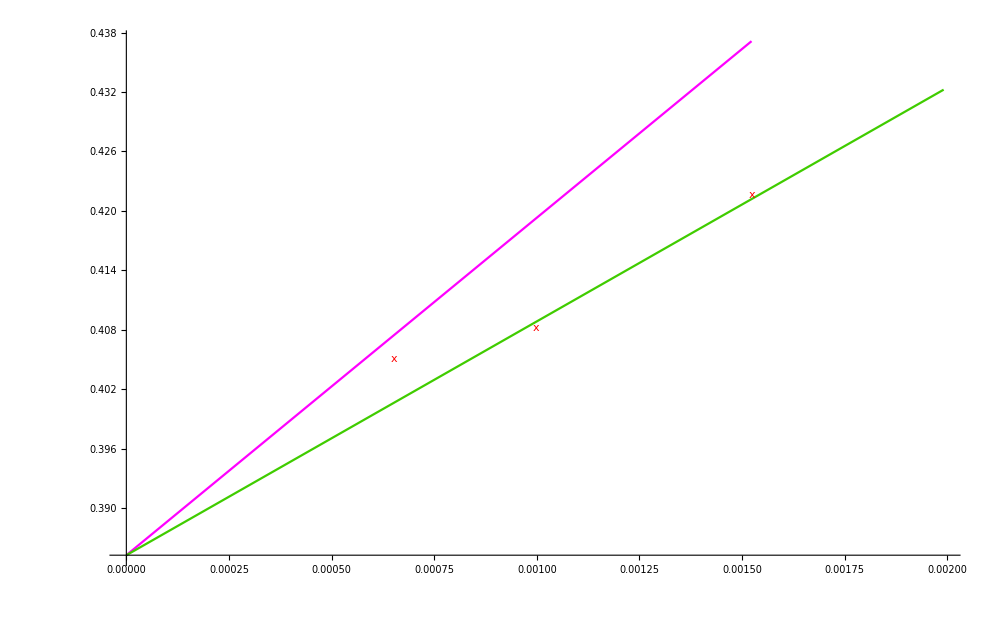

{0.3751,0.37159,0.382903}

```mathematica
λ[r_]:=(1+2.1 r/R)(1+3.3 r/H)
λe[r_]:=(1+2.1 r/R)
Ladengerade[r_]:=a*λe[r]
PlotLad:=Plot[Ladengerade[r],{r,0,Max[xvalues]},PlotStyle->Magenta]
Show[PlotLad,PlotGer,PlotPoin, PlotRange->All,ImageSize->{1000,800}(*,PlotRange->{Min[yvalues]*0.99,Max[yvalues]*1.01}*)]
LadenkorrigierteWerte:=Table[yvalues[[i]]/λe[xvalues[[i]]],{i,1,n}]
LadenkorrigierteWerte
```

## Relative Fehler:

```mathematica
relFehl=Table[errys[[i]]/yvalues[[i]],{i,1,n}]
```

{0.0142087,0.0315052,0.0444432}

```mathematica
σb
```

```mathematica
errsquasum*xsquasumwe-xsumwe^2
```

174.618

```mathematica
Δ
```

174.618